```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
(************** LT plot *****************************)
```

```mathematica
LTData=Import["LTplot.dat"];
temp=LTData[[All,1]];(*Temp in kelvin*);
Lum=LTData[[All,2]];(* erg s^-1*);
```

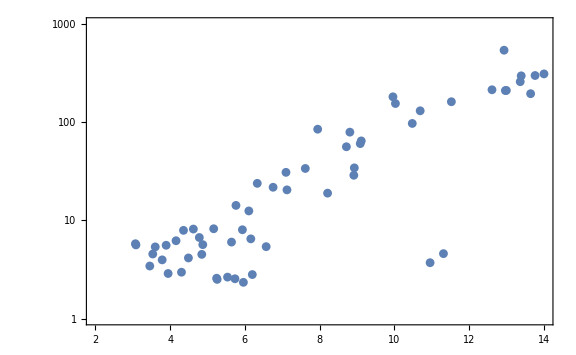

```mathematica
ListLogPlot[LTData,PlotRange->{{2,14},{1,1000}}, Frame->True,ImageSize->Large]
```

```mathematica
vbar=20*10^3;(*in m/sec*)
G=6.67*10^-11;(*in SI*)(*m^3 kg^-1 s^-2*)
ρ=10^11;(*in kg/m^3*)
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
t=3 10^17(*Age in sec*);
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
(************************** Definitions ***********************************)
Nn[R_,nn_]:=4/3 π R^3 nn
sigmaSat[R_,nn_]:=(π R^2)/Nn[R,nn]
```

```mathematica
sigmaSat[9 10^6,10^36.]
```

8.33333×10^-44

```mathematica
rth[mx_,T_]:=((9kb T)/(4 π G ρ mx 1.78 10^-27))^0.5;
vth[mx_,T_]:=4/3 π rth[mx,T]^3;
```

```mathematica
mr[mx_,mn_]:=(mn mx)/(mn+mx);
δp[mx_,mn_,vesc_]:=2^0.5*mr[mx,mn]*vesc*1.78*10^-27;(*vesc in m/sec, and the whole term in kg m /sec *)
hbar=(6.626*10^-34)/(2*3.14);(*kg m^2 /sec *)
pf[n_]:=hbar(3 π^2 n)^(1/3); (*kg m / sec *)
```

```mathematica
(*SINGLE SCATTERING*)
```

```mathematica
asq[mx_,mn_,vesc_]:=3/2 vesc^2/vbar^2 (4 mx mn)/(mx-mn)^2;
b[mx_,sigmaself_,vesc_]:=(ρx/mx(6/π)^0.5 sigmaself vbar (vesc^2/vbar^2-2/3));
a[mx_,mn_,R_,sigma_,n_,vesc_]:=If[asq[mx,mn,vesc]≤26,(ρx/mx(6/π)^0.5 Min[sigma,sigmaSat[R,n]]Min[1,δp[mx,mn,vesc]/pf[n]]vbar Nn [R,n] vesc^2/vbar^2(1-(1-Exp[-asq[mx,mn,vesc]])/asq[mx,mn,vesc])),(ρx/mx(6/π)^0.5 Min[sigma,sigmaSat[R,n]]Min[1,δp[mx,mn,vesc]/pf[n]]vbar Nn [R,n] vesc^2/vbar^2(1-1/asq[mx,mn,vesc]))];
```

```mathematica
f[x_]:=1-(1-Exp[-x^2])/x^2
g[x_]:=1-1/x^2
```

```mathematica
ldm[mx_,mn_,sigma_,sigmaself_,anncross_,R_,n_,T_,vesc_]:=mx(a[mx,mn,R,sigma,n,vesc]+b[mx,sigmaself,vesc](b[mx,sigmaself,vesc]+(b[mx,sigmaself,vesc]^2+4a[mx,mn,R,sigma,n,vesc] anncross/vth[mx,T])^0.5)/(2 anncross/vth[mx,T]));
```

```mathematica
ldm[10,12.,10^-40,10^-34,10^-42,7 10^6,10^36,10^4,6 10^6]
```

3.8293×10^32

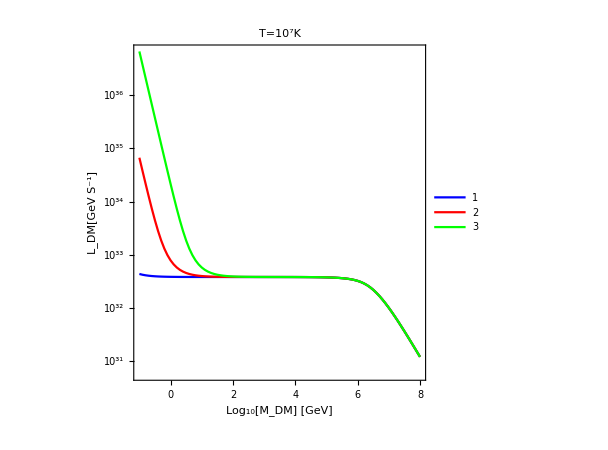

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,12.0,sigmaSat[7 10^6,10^36],1/(5.62*10^27),3 10^-32,7 10^6,10^36,10^7,6 10^6]},{x,-1,8,0.1}],
Table[{x,ldm[10^x,12.0,sigmaSat[7 10^6,10^36],1/(5.62*10^27),3 10^-36,7 10^6,10^36,10^7,6 10^6]},{x,-1,8,0.1}],Table[{x,ldm[10^x,12.0,sigmaSat[7 10^6,10^36],1/(5.62*10^27),3 10^-38,7 10^6,10^36,10^7,6 10^6]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameLabel->{Style[" Log_10[M_DM] [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM[GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450, PlotLegends->Automatic,PlotLabel->"T=10^7K"]
```

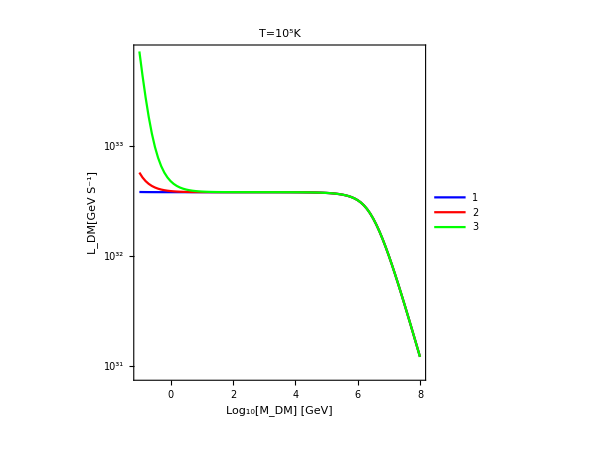

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,12.0,sigmaSat[7 10^6,10^36],1/(5.62*10^27),3 10^-32,7 10^6,10^36,10^5,6 10^6]},{x,-1,8,0.1}],
Table[{x,ldm[10^x,12.0,sigmaSat[7 10^6,10^36],1/(5.62*10^27),3 10^-36,7 10^6,10^36,10^5,6 10^6]},{x,-1,8,0.1}],Table[{x,ldm[10^x,12.0,sigmaSat[7 10^6,10^36],1/(5.62*10^27),3 10^-38,7 10^6,10^36,10^5,6 10^6]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameLabel->{Style[" Log_10[M_DM] [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM[GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450, PlotLegends->Automatic,PlotLabel->"T=10^5K"]
```

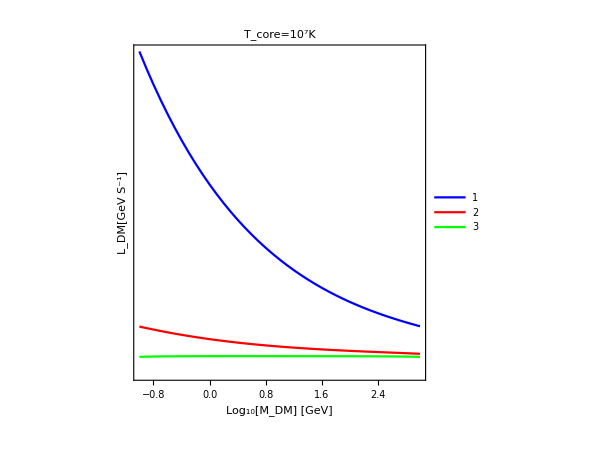

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,12.0,10^-44,10^x/(5.62*10^27),10^-32,7 10^6,10^36,10^7,6 10^6]},{x,-1,3,0.1}],
Table[{x,ldm[10^x,12.0,10^-44,(0.1 10^x)/(5.62*10^27),10^-32,7 10^6,10^36,10^7,6 10^6]},{x,-1,3,0.1}],Table[{x,ldm[10^x,12.0,10^-44,(0.001 10^x)/(5.62*10^27),10^-32,7 10^6,10^36,10^7,6 10^6]},{x,-1,3,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameLabel->{Style[" Log_10[M_DM] [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM[GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450, PlotLegends->Automatic,PlotLabel->"T_core=10^7K"]
```

```mathematica
conversionfactor=6.24 10^9;(*Joule to GeV*)
σ0=5.67 10^-8;
```

```mathematica
MyRadUnsort=Table[r1=((Lum[[i]]624.15 10^28)/(4π conversionfactor σ0 (temp[[i]]10^3)^4))^0.5,{i,1,Length[temp]}];(*in mtr*)
```

```mathematica
LTmytable=Table[{r1=MyRadUnsort[[i]]/10^6,lum1=Lum[[i]]624.15,Temp=temp[[i]]},{i,1,Length[temp]}];
```

```mathematica
Export["LTheatPlot.dat",LTmytable];
```

```mathematica
MyRad=Sort[Table[r1=((Lum[[i]]624.15 10^28)/(4π conversionfactor σ0 (temp[[i]]10^3)^4))^0.5,{i,1,Length[temp]}]];(*in mtr and SORTED*)
```

```mathematica
mdm=10.(*GeV*);
sigma=10^-44(*m^2*);
sigmaself=10^-27;(*m^2*)
anncross=10^-38;(*m^3/s*)
LDMtable=Table[{r1=10^i,lum2=1/10^28 ldm[mdm,5 10^-3,sigma,sigmaself,anncross,r1 10^6,10^36,10^6,6 10^6]},{i,-4,1,0.1}];
```

```mathematica
sigmaSatTable=Table[{r1=10^i,sigmasat=sigmaSat[r1*10^6,10^36],lum3=1/10^28  ldm[mdm,5 10^-3,sigmasat,sigmaself,anncross,r1 10^6,10^36,10^6,6 10^6]},{i,-4,1,0.1}];
```

```mathematica
Export["dataSigmaSat.dat",sigmaSatTable];
```

```mathematica
Export["data2.dat",LDMtable];
```

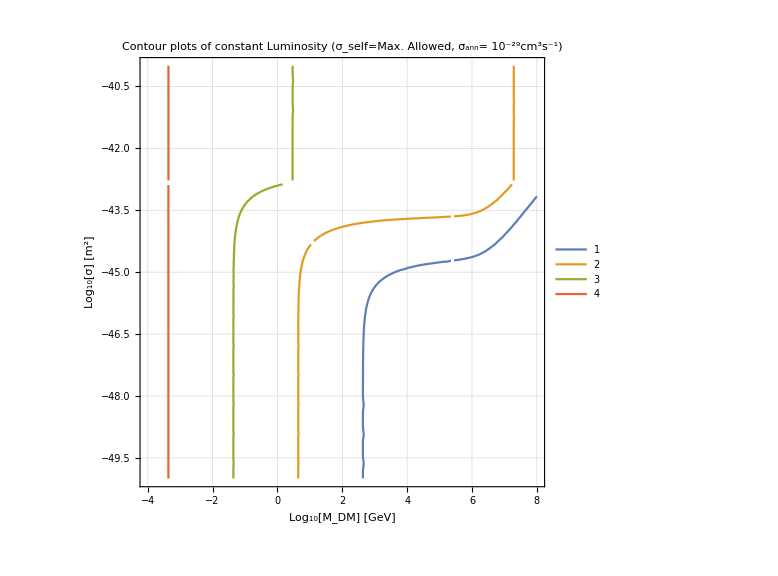

```mathematica
cntrplot3=ContourPlot[{ldm[10^mdm,12.,10^sigma,10^mdm 10^-27,10^-35,5 10^6,10^36,10^6,6 10^6]==3 10^30,ldm[10^mdm,12.,10^sigma,10^mdm 10^-27,10^-35,5 10^6,10^36,10^6,6 10^6]==3 10^31,ldm[10^mdm,12.,10^sigma,10^mdm 10^-27,10^-35,5 10^6,10^36,10^6,6 10^6]==3 10^32,ldm[10^mdm,12.,10^sigma,10^mdm 10^-27,10^-35,5 10^6,10^36,10^6,6 10^6]==3 10^33},{mdm,-4,8},{sigma,-40,-50},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant Luminosity (σ_self=Max. Allowed, σ_ann= 10^-29cm^3s^-1)",FontSize->8,Bold],GridLines->Automatic]
```

```mathematica
(*points=Catenate@Cases[Normal@cntrplot1,Line[pts_]->pts,Infinity];
cntrTable=Flatten/@Flatten[PadRight[points,Automatic,""],{2}];
Export["file2.txt",points,"Table"];*)
```

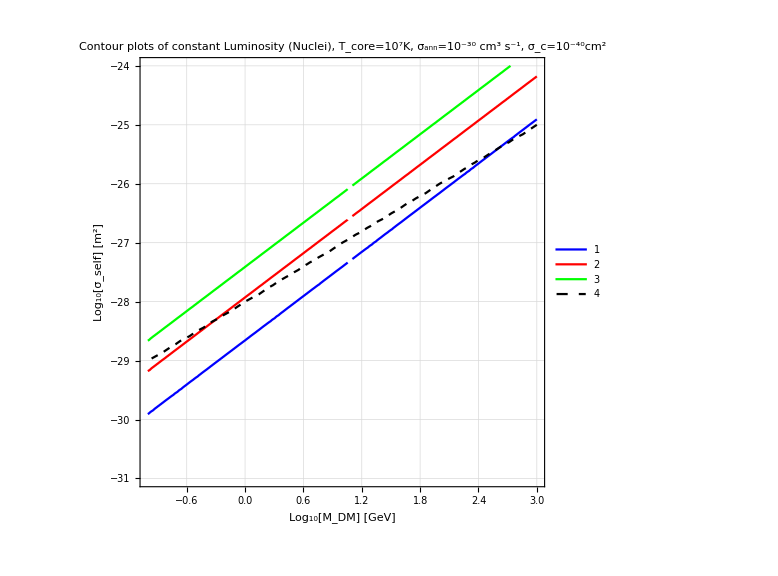

```mathematica
cntrplot1=ContourPlot[{ldm[10^mdm,12.,10^-44,10^sigmaself,10^-36,5 10^6,10^36,10^7,6 10^6]==3 10^31,ldm[10^mdm,12.,10^-44,10^sigmaself,10^-36,5 10^6,10^36,10^7,6 10^6]==3 10^32,ldm[10^mdm,12.,10^-44,10^sigmaself,10^-36,5 10^6,10^36,10^7,6 10^6]==3 10^33,10^sigmaself/10^mdm==10^-28},{mdm,-1,3},{sigmaself,-24,-31},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[σ_self] [m^2]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant Luminosity (Nuclei), T_core=10^7K, σ_ann=10^-30 cm^3 s^-1, σ_c=10^-40cm^2",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}}]
```

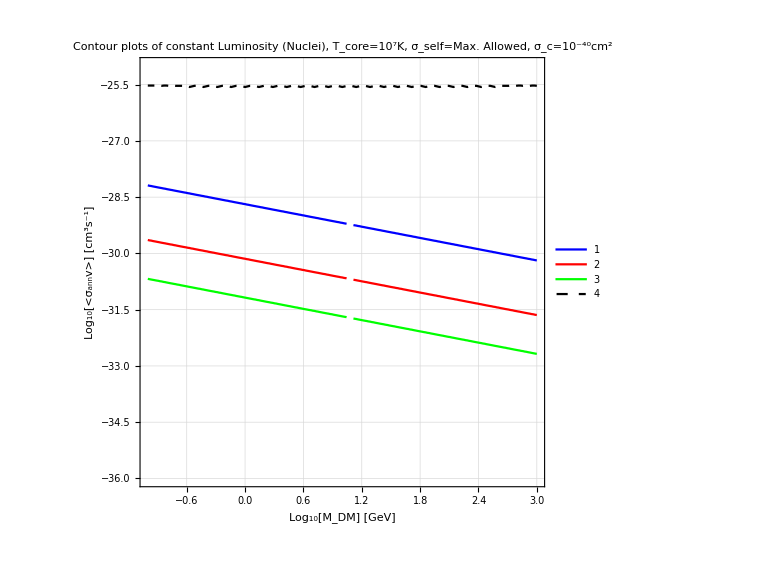

```mathematica
cntrplot2=ContourPlot[{ldm[10^mdm,12.,10^-44,10^mdm 10^-27,10^-4 10^sigmaAnn,5 10^6,10^36,10^7,6 10^6]==3 10^31,ldm[10^mdm,12.,10^-44,10^mdm 10^-27,10^-4 10^sigmaAnn,5 10^6,10^36,10^7,6 10^6]==3 10^32,ldm[10^mdm,12.,10^-44,10^mdm 10^-27,10^-4 10^sigmaAnn,5 10^6,10^36,10^7,6 10^6]==3 10^33,10^sigmaAnn==3 10^-26},{mdm,-1,3},{sigmaAnn,-25,-36},PlotLegends->Automatic,ContourLabels->All,Frame->True,FrameStyle->Directive[14,"Times",Black],FrameLabel->{Style["Log_10[M_DM] [GeV]",FontSize->20,Bold],Style["Log_10[<σ_annv>] [cm^3s^-1]",FontSize->20,Bold]},ImageSize -> Large,PlotLabel->Style["Contour plots of constant Luminosity (Nuclei), T_core=10^7K, σ_self=Max. Allowed, σ_c=10^-40cm^2",FontSize->8,Bold],GridLines->Automatic,ContourStyle->{{Thick,Blue},{Thick,Red},{Thick,Green},{Thick,Dashed,Black}}]
```

```mathematica
Export["cntrplot3.pdf",cntrplot2];
```